## Introduction

Young diagrams are a graphical technique that can be convenient for finding features of representations of Lie algebras of kinds of matrices: SU(n), SO(n), Sp(n) for size parameter n. This notebook implements several Young-diagram algorithms.

In the code, they come in four kinds, with these abbreviations:
Xp -- expanded Young diagrams: list of lists of values, default Null
Ct -- contracted Young diagrams: list of row lengths
Wvr -- variable-length weight vectors
Wfx -- fixed-length weight vectors (size parameter from their length)

When converting, the code eliminates trailing empty rows to make the first and second ones, and trailing zeros to make the third one. The code will add trailing zeros to make the fourth one.

SU(n) is special unitary matrices, related to SL(n,R), special linear real matrices, by analytic continuation. Representations are tensors, multi-index entities, with scalars zero indices and vectors one index. The irreducible ones are tensors with various symmetries.

SO(n) is special orthogonal matrices, like SU(n) but with tensor reps traceless with respect to the algebra metric, a symmetric matrix.

Sp(n) is symplectic matrices, like SO(n) but with an antisymmetric matrix instead of a symmetric one.

Several of the verifiers use notebook Semisimple Lie Algebras.nb referred to here as SSLA

### Young-Diagram Operations

Conversion Operations

For expanded Young:
func = labeling function, with args (row #),(col #), counted from 1 - default: returns Null
For fixed-length weights:
n = number of weights - for SU(n+1)

YDConvertXpCt[ydgm_] -- expanded to contracted Young
YDConvertCtXp[ydgm_,func_] -- contracted to expanded Young
YDConvertCtWvr[yrls_] -- contracted Young to variable-length weights
YDConvertWvrCt[vwts_] -- variable-length weights to contracted Young
YDConvertWvrWfx[vwts_,n_] -- variable-length to fixed-length weights
YDConvertWfxWvr[fwts_] -- fixed-length to variable-length weights
YDConvertXpWvr[ydgm_] -- expanded Young to variable-length weights
YDConvertWvrXp[vwts_,func_] --  variable-length weights to expanded Young
YDConvertCtWfx[yrls_,n_] -- contracted Young to fixed-length weights
YDConvertWfxCt[fwts_] -- fixed-length weights to contracted Young
YDConvertXpWfx[ydgm_,n_] -- expanded Young to fixed-length weights
YDConvertWfxXp[fwts_,func_] -- fixed-length weights to expanded Young

Other

YDRelabelXp[ydgm_,func_] -- relabels an expanded diagram with a labeling function with args row, column

Transposes a Young diagram to find its dual
YDTransposeXp[ydgm_] -- expanded Young
YDTransposeCt[yrls_]  -- contracted Young

### Degeneracy (Rep Size): SU(n), SO(n), Sp(n)

DegenFxd[type_,fwts_] - fixed-length weights (may be symbolic)
Types: SU(n), SO(2n), SO(2n+1), Sp(2n)

DegenCt[type_,yrls_,n_] - contracted Young diagram, for matrix size n that may be symbolic
Types: SU(n), SO(n), Sp(n)
Warning: this may not work properly if n is too small.

DegenXp[type_,ydgm_,n_] - like the above, but with expanded diagrams

DegenCtTest[type_,yrls_,n_] - contracted Young diagram, for integer n - length of fixed weights. Uses SSLA
Types: SU(n), SO(2n), SO(2n+1), Sp(2n)

### Representation Products - SU(n)

Implements the Littlewood-Richardson rule for decomposing product representations into irreps.

YDProductXp[dgrm1_, dgrm2_] takes two expanded diagrams creates a list of expanded product diagrams that are labeled according to the algorithm. 0 = first diagram and 1,2,3,... = rows of second diagram.

YDProductXpVerify[dgrm1_,dgrm2_,n_] does the above, and also finds rep dimensions using SU(n) dimension n (may be symbolic). It then multiplies and adds as appropriate, emitting all the diagrams and dimension values.

YDProductCt[dgrm1_, dgrm2_] takes two contracted diagrams and creates a list of {multiplicity, contracted product diagram}.

YDProductCtVerify[dgrm1_,dgrm2_,n_] is like the earlier verify function

### Vector-Representation Powers - SU(n)

These are useful for decomposing by symmetry.

VPFindMultDgrmList[p_] decomposes power p of the vector or fundamental representation of SU(n). It makes a list with form {multiplicity, contracted Young diagram}, and they have the order (most symmetric) to (most antisymmetric).

VPFindDgrmList[p_] finds only the diagrams for power p, without their multiplicities.

VPFindMultDgrmListSeq[pmax_] finds a list of VPFindMultDgrmList[] for powers from 1 to pmax.

VPFindDgrmListSeq[pmax_] finds a list of VPFindDgrmList[] for powers from 1 to pmax.

### Weyl Orbits - SU(n)

In group theory, an “orbit” is a set of entities related by permutations induced by the elements of a group, such that this set does not have nontrivial subsets with this property.

For Lie algebras, one tags the members of the basis set of a representation with the values for applying a commuting subset, the “Cartan subalgebra”, giving the rep’s “roots”. Quantum-mechanical angular momentum has a simple example of this. All roots related by reflection in the root space form an orbit, the “Weyl orbit”. Each Weyl orbit is designated the same way as an irrep is, with its highest-weight vector.

An irrep typically contains more than one Weyl orbit, but Weyl orbits are often relatively easy to generate.

Degeneracy: SU(n)

WeylOrbitDegenSUnCt[yrls_,n_] -- contracted Young. How many members of a Weyl orbit. The first arg can be a list of symbols and second one symbolic.

WeylOrbitDegenSUnCtVerify[pmax_,n_] -- uses SSLA, maximum power pmax, weight-vector size n.
WeylOrbitDegenSUnCtVerify[n_] uses pmax = n

Irreps: Counts of Weyl Orbits: SU(n) finds the multiplicity of each Weyl orbit in an irrep, the “Kostka matrix”.

KostkaMatrix[p_] finds the Kostka matrix for power p. Rows: irreps, columns: Weyl orbits. The function uses the ordering of Young diagrams in VPFindDgrmList[p], to give a triangular matrix.

KostkaMatrices[pmax_] finds a list of Kostka matrices for powers from 1 to p.

KostkaMatrixVerify[pmax_,n_] uses SSLA, maximum power pmax, weight-vector size n.
KostkaMatrixVerify[n_] uses pmax = n

KostkaMatrixSizeVerify[pmax_,n_] for maximum power nmax and matrix size n, which can be symbolic.

SU(n) Weyl-Orbit Products and Powers - NOT VERIFIED

WeylOrbitProductSUnCt[yrls1_,yrls2_] takes two contracted Young diagrams, and finds a list of product Weyl orbits as a list of {multiplicity, contracted Young}

SU(n) Branching Rules - NOT VERIFIED

WeylOrbitBranchingSUnCt[n1_, n2_, maxwt_] args n1 of SU(n1), n2 of SU(n2), maxwt of original algebra, SU(n1+n2). Makes list of SU(n1) highest weight, SU(n2) highest weight, U(1) factor.

Handle SU(n) -> SU(n-1)*U(1) by treating it as SU(n-1)*SU(1)*U(1).

### Branching Rules

These are how one finds subalgebra representations from Lie-algebra reps.

Implemented here:
SU(n) -> SO(n) and Sp(n)

For SU(n) -> SO(n) one takes a tensor rep of SU(n) and finds it as a sum of products of traceless tensors - reps of SO(n) - and products of the matrix invariant for SO(n), like
X(i,j) = X(traceless,i,j) + delta(i,j)*X(scalar)
X(i,j,k) = X(traceless,i,j,k) + delta(i,j)*X(vector,k) + delta(i,k)*X(vector,j) + delta(j,k)*X(vector,i)
where the SO(n) matrix invariant delta(i,j) is the Kronecker delta, equal to 1 for i = j, 0 for i != j.

That delta has contracted Young diagram {2} and its tensor products are 2*(contracted Young diagrams).
Thus, {1} -> {1} and {2} -> {2} and {} (multiplied by {2}), and {1,1} -> {1,1}

SU(n) -> Sp(n) like for SO(n) but with the matrix invariant’s Young diagrams transposed, from the matrix invariant being an antisymmetric tensor.
Thus, {1} -> {1} and {2} -> {2}, and {1,1} -> {1,1} and {} (multiplied by transpose of {2}: {1.1})

There are also inverse formulas for these two cases, but I have found them difficult to understand.

SUSOSpBranching[pmax_,flip_:False]
returns an association of all YD’s up to size pmax with their breakdowns as counted lists. SO(n): flip = False, Sp(n): flip = True.

SUSOSpFwdInvBranching[pmax_,flip_:False]
returns both that association and an association of inverse transforms, getting SU(n) from SO(n) and Sp(n).

One can use that transform and its inverse to do products of SO(n) and Sp(n) reps as Young diagrams.

Additional ones, though not implemented here:
SO(n) -> U(k) * SO(n-2k) -- k = 1 to floor(n/2)-1
Sp(n) -> U(k) * Sp(n-2k) -- k = 1 to floor(n/2)-1
SO(n) -> SO(k) * SO(n-k) -- k = 1 to n-1
Sp(n) -> Sp(k) * Sp(n-k) -- k = 2 to n-2 by 2

### Nesting

YDNesting[p_] finds the YD nesting matrix for power p. Rows and columns are indexed by the YD’s for power p. For the row YD, take its row lengths and find the YD’s for each of the length. Take one each and concatenate them to form a YD that is the column YD. Add to the matrix’s entry at that location the indices of each of these YD’s.

YDNestings[pmax_] finds a list of YD nesting matrices for powers from 1 to pmax.

### Symmetrized Powers and Related Entities

#### Symmetric and Alternating Group Characters

Symmetric group: group of all permutations with some size.
Conjugacy classes: all permutations with some set of cycle sizes.
Irreps: also designated with those sets of cycle sizes.

Alternating group: group of all even permutations with some size.
Conjugacy classes: some symmetric-group ones are dropped, some are split
Irreps: some are merged, some are split

SymmGroupCharacters[nmax_] -- up to size nmax

SymmGroups[nmax_,flip_:True] -- list of associations with keys “Index” (size), “Perms” (permutation sizes), “Degens” - (degeneracies: sizes of permutation classes), “Chars” (character table)

MakeAltGroup[symgrp_] -- from symmetric-group association: an association with keys  “Index”, “Classes”, “Degens”, “Irreps”, “Chars”

#### Symmetric Polynomials

Symmetric polynomial - Wikipedia
https://en.wikipedia.org/wiki/Symmetric_polynomial
Newton’s identities - Wikipedia
https://en.wikipedia.org/wiki/Newton%27s_identities

PwrSumFromList[n_,xlst_] -- sum of powers n of xlst
PwrSumListFromList[nmax_,xlst_] -- sums from 1 to nmax
x1+x2, x1^2+x2^2, x1^3+x2^3

Elementary symmetric polynomials:
PwrSumToElmSym[pslst_] -- power sums to ESP’s
ElmSymToPwrSum[eslst_] -- ESP’s to power sums
x1+x2, x1*x2, 0

Homogeneous symmetric functions:
PwrSumToHomSym[pslst_] -- power sums to HSP’s 
HomSymToPwrSum[hslst_] -- HSP’s to power sums
x1+x2, x1^2+x1*x2+x2^2, x1^3+x1^2*x2+x1*x2^2+x2^3

Elementary - homogeneous interchange:
ElmSymHomSymItchg[islst_]

These identities can be proved using generating functions.

#### Schur Polynomials

An additional kind of symmetric polynomial, related to the Lie-algebra character function for SU(n), and also to the character matrix for the symmetric group.

yrls: contracted Young diagram
xlst: list of variables to take powers of
SchurDet[yrls_,xlst_] -- calculated from the determinant definition
SchurHomSym[yrls_,hs_] -- calculated from homogeneous symmetric polynomials (Jacobi-Trudi identity 1)
SchurHomSymList[yrls_,xlst_] -- from a starting list
SchurElmSym[yrls_,hs_] -- calculated from elementary symmetric polynomials (Jacobi-Trudi identity 2)
SchurElmSymList[yrls_,xlst_] -- from a starting list

KostkaSchur[pmax_,xlst_] -- finds monomial symmetric polynomials: x1^p1*x2^p2*... for diagrams {p1,p2,...} for diagram sizes from 1 to pmax
Uses order in VPFindDgrmListSeq[pmax]

MultiSchurPowerSum[pmax_,xlst_] -- finds those Schur polynomials, using the symmetric-group characters

Schur(yd1,xlst) * Schur(yd2,ylst) = sum over yd of (Littlewood-Richardson coefficient for yd1 and yd2 to yd) * Schur(yd,xlst)
The L-R coefficient is implemented here in YDProductCt[yd1,yd2]

#### Plethysms - Symmetrized Powers

SelYDPlethysm[pthsel_,pthnmax_,sel_,nmax_]
Args: Selection and max power of plathysmer, selection and max power of plethysmed one
Plethysmer: symmetrized power to be applied
Plethysmed one: what is applied to

Selectors:
Sym -- symmetric, max power
SymAll -- symmetric, all powers
Ats -- antisymmetric, max power
AtsAll -- antisymmetric, all powers
Gen -- general, max power
GenAll -- general, all powers

Returns: a matrix with each row having a plethysmed value and each column having a plethysmer. Each row-column location contains a result as a counted list of contracted YD’s.

### Graphics

Graphics objects:
YDGraphObjectXp[dgrm_] -- expanded YD with box contents displayed
YDGraphObjectCt[yrls_] -- contracted YD with boxes empty

Graphics displays:
YDGraphDisplayXp[dgrm_,size_] -- like above Xp one, with display canvas size “size”
YDGraphDisplayCt[yrls_,size_] -- like above Ct one, with display canvas size “size”

### Sources

Particle Data Group: http://pdg.lbl.gov > Reviews > Mathematical Tools > SU(n) multiplets and Young diagrams

Littlewood–Richardson rule - Wikipedia
https://en.wikipedia.org/wiki/Littlewood%E2%80%93Richardson_rule

Young-Diagrammatic Methods for the Representation Theory of the Classical Groups of Type Bn, Cn, Dn
KAZUHIKO KOIKE, ITARU TERADA
https://core.ac.uk/download/pdf/82707198.pdf

On the Decomposition of Tensor Products of the Representations of the Classical Groups: By Means of the Universal Characters
KAZUHIKO KOIKE
https://core.ac.uk/download/pdf/82598102.pdf

Young Diagrammatic Methods for the Restriction of Representations of Complex Classical Lie Groups to Reductive Subgroups of Maximal Rank
KAZUHIKO KOIKE, ITARU TERADA
https://core.ac.uk/download/pdf/82311123.pdf

Kostka number - Wikipedia
https://en.wikipedia.org/wiki/Kostka_number

Kostka-matrix algorithm from
Determinantal Expression and Recursion for Jack Polynomials | The Electronic Journal of Combinatorics
https://www.combinatorics.org/ojs/index.php/eljc/article/view/v7i1n1

## Young-Diagram Operations

```mathematica
(* Expanded Young < - > contracted Young *)
```

```mathematica
NullFunc[___] := Null
```

```mathematica
YDConvertXpCt[ydgm_] := Length /@ ydgm
```

```mathematica
YDConvertCtXp[yrls_,func_:NullFunc] := Table[func[iv,ih],{iv,Length[yrls]},{ih,yrls[[iv]]}]
```

```mathematica
(* Contracted Young < - > variable weights *)
```

```mathematica
YDConvertCtWvr[yrls_] := -Differences[Append[yrls,0]]
```

```mathematica
YDConvertWvrCt[vwts_] := Reverse[Accumulate[Reverse[vwts]]]
```

```mathematica
(* Variable weights < - > fixed weights *)
```

```mathematica
YDConvertWvrWfx[vwts_,n_Integer] := If[Length[vwts] < n,PadRight[vwts,n],Take[vwts,n]]
```

```mathematica
YDConvertWfxWvr[fwts_] := If[Length[fwts] > 0,If[Last[fwts]===0,YDConvertWfxWvr[Most[fwts]],fwts],{}]
```

```mathematica
(* Expanded Young < - > variable weights *)
```

```mathematica
YDConvertXpWvr[ydgm_] := YDConvertCtWvr[YDConvertXpCt[ydgm]]
```

```mathematica
YDConvertWvrXp[vwts_,func_:NullFunc] := YDConvertCtXp[YDConvertWvrCt[vwts],func]
```

```mathematica
(* Contracted Young < - > fixed weights *)
```

```mathematica
YDConvertCtWfx[yrls_,n_Integer] := YDConvertWvrWfx[YDConvertCtWvr[yrls],n]
```

```mathematica
YDConvertWfxCt[fwts_] := YDConvertWvrCt[YDConvertWfxWvr[fwts]]
```

```mathematica
(* Expanded Young < - > fixed weights *)
```

```mathematica
YDConvertXpWfx[ydgm_,n_Integer] := YDConvertWvrWfx[YDConvertCtWvr[YDConvertXpCt[ydgm]],n]
```

```mathematica
YDConvertWfxXp[fwts_,func_:NullFunc] := YDConvertCtXp[YDConvertWvrCt[YDConvertWfxWvr[fwts]],func]
```

```mathematica
(* Relabeling an expanded Young diagram *)
```

```mathematica
YDRelabelXp[ydgm_,func_:NullFunc] := Table[func[iv,ih],{iv,Length[ydgm]},{ih,Length[ydgm[[iv]]]}]
```

```mathematica
(* Transposes a Young diagram to find its dual *)
```

```mathematica
YDTransposeXp[ydgm_] :=Module[{n1,n2,newydgm,i1,i2},
(* i1, i2, n1, n2 reloative to original *)
n1 = Length[ydgm];n2 = Max[Length /@ ydgm];
newydgm=Table[{},{n2}];
Do[AppendTo[newydgm[[i2]],ydgm[[i1,i2]]],{i1,n1},{i2,Length[ydgm[[i1]]]}];
newydgm]
```

```mathematica
YDTransposeCt[yrls_] := Module[{nyrs,yrdf,i},
nyrs = Length[yrls];
yrdf = Differences[Reverse[Append[yrls,0]]];
Flatten[Table[Table[nyrs-i+1,{yrdf[[i]]}],{i,nyrs}],1]
]
```

## Degeneracy (Rep Size) - SU(n), SO(n), Sp(n)

```mathematica
(* Fixed-length weights. Can be symbolic. *)
```

```mathematica
DegenFxd["SU(n)",fwts_] := Product[(Total[Take[fwts,{l,l+k-1}]]+k)/k,{k,Length[fwts]},{l,Length[fwts]-k+1}]
```

```mathematica
DegenFxd["SO(2n)",fwts_] := DegenFxd["SU(n)",Most[fwts]]*Product[(Total[Take[fwts,{-k-2,-3}]]+Last[fwts]+(k+1))/(k+1),{k,0,Length[fwts]-2}]*Product[(Total[Take[fwts,{-k-l-2,-k-3}]]+Expand[2*Total[Take[fwts,{-k-2,-3}]]]+Last[Most[fwts]]+Last[fwts]+(2k+l+2))/(2k+l+2),{k,0,Length[fwts]-2},{l,1,Length[fwts]-k-2}]
```

```mathematica
DegenFxd["SO(2n+1)",fwts_] := DegenFxd["SU(n)",fwts]*Product[(Total[Take[fwts,{-k-l-1,-k-2}]]+Expand[2*Total[Take[fwts,{-k-1,-2}]]]+Last[fwts]+(2k+l+1))/(2k+l+1),{k,1,Length[fwts]-1},{l,0,Length[fwts]-k-1}]
```

```mathematica
DegenFxd["Sp(n)",fwts_] := DegenFxd["SU(n)",fwts]*Product[(Total[Take[fwts,{-k-l-1,-k-2}]]+Expand[2*Total[Take[fwts,{-k-1,-2}]]]+2*Last[fwts]+(2k+l+2))/(2k+l+2),{k,0,Length[fwts]-1},{l,1,Length[fwts]-k-1}]
```

```mathematica
(* Test that uses SSLA*)
```

```mathematica
DegenFxdTestType = <|"SU(n)"->1,"SO(2n+1)"->2,"Sp(2n)"->3,"SO(2n)"->4|>;
```

```mathematica
DegenFxdTest[type_,fwts_] := DegenFxd[type,fwts]/TotalDegen[{DegenFxdTestType[type],Length[fwts]},fwts,False]
```

```mathematica
(* Calculations for Young diagrams - contracted ones - where n can be symbolic *)
```

```mathematica
YDHookCt[yrls_] := Module[{dual},
dual = YDTransposeCt[yrls];
Product[1+(yrls[[i]]-i)+(dual[[j]]-j),{i,Length[yrls]},{j,yrls[[i]]}]
]
```

```mathematica
DegenCt["SU(n)",yrls_,n_] := (Times @@ Flatten[YDConvertCtXp[yrls,n-#1+#2&],2])/YDHookCt[yrls]
```

```mathematica
DegenCt["SOSp(n)",yrls_,q_,n_] := Module[{yrllen,yrx,nx},
yrllen = Length[yrls];
yrx[i_] := If[i>0&&i<=yrllen,yrls[[i]],0];
Factor[Product[(nx-2i-j+q+1+yrx[i]+yrx[i+j+q-1]),{i,yrllen},{j,yrls[[i]]}]*
Product[(nx-2i-j+q+yrx[i+yrx[i]+j+q])/(nx-2i-j+q),{i,yrllen},{j,0,yrllen-i-yrx[i]}]]/YDHookCt[yrls] /. nx->n
]
```

```mathematica
DegenCt["SO(n)",yrls_,n_] := DegenCt["SOSp(n)",yrls,0,n]
```

```mathematica
DegenCt["Sp(n)",yrls_,n_] := DegenCt["SOSp(n)",yrls,1,n]
```

```mathematica
(* n must be an integer here *)
```

```mathematica
DegenCtTest["SU(n)",yrls_,n_] := {DegenCt["SU(n)",yrls,n+1], DegenFxd["SU(n)",YDConvertCtWfx[yrls,n]]}
```

```mathematica
DegenCtTest["SO(2n)",yrls_,n_] := {DegenCt["SO(n)",yrls,2n], DegenFxd["SO(2n)",YDConvertCtWfx[yrls,n]]}
```

```mathematica
DegenCtTest["SO(2n+1)",yrls_,n_] := {DegenCt["SO(n)",yrls,2n+1], DegenFxd["SO(2n+1)",YDConvertCtWfx[yrls,n]]}
```

```mathematica
DegenCtTest["Sp(2n)",yrls_,n_] := {DegenCt["Sp(n)",yrls,2n], DegenFxd["Sp(2n)",YDConvertCtWfx[yrls,n]]}
```

```mathematica
(* Convert to other types of Young-diagram data *)
```

```mathematica
DegenXp[type_,ydgm_,n_] := DegenCt[type,YDConvertXpCt[ydgm],n]
```

## Representation Products - SU(n)

```mathematica
(* Product of reps; uses the Littlewood-Richardson rule. *)
```

```mathematica
(* Auxiliary functions. These work with expanded diagrams *)
```

```mathematica
ClipEmpty[dgrm_] := Module[{k,newdgrm},
newdgrm = dgrm;
Do[If[Length[dgrm[[k]]] ==0,newdgrm = Take[dgrm,k-1]; Break[]],{k,Length[dgrm]}];
newdgrm]
```

```mathematica
YDAddOne[dgrm_,token_,start_] := Module[{outlist,olddgrm,newdgrm,k,apnd,ndlen},
(* token must be absent from the original diagram *)
olddgrm = Append[dgrm,{}];
outlist = {};
Do[newdgrm = olddgrm;
AppendTo[newdgrm[[k]],token];
ndlen = Length[newdgrm[[k]]];
If[k > 1, apnd = ndlen ≤ Length[newdgrm[[k-1]]],apnd = True];
If[apnd,Do[If[newdgrm[[l,ndlen]]===token,apnd = False; Break[]],{l,k-1}]];
If[apnd,AppendTo[outlist,{newdgrm,k}]],{k,start,Length[olddgrm]}];
outlist = {ClipEmpty[#[[1]]],#[[2]]}& /@
outlist]
```

```mathematica
YDAddSet[dgrm_, token_, number_] :=
Module[{oldlist,outlist,newlist,k,l,oldmem},
(* token must be absent from the original diagram *)
outlist = {{dgrm,1}};
oldlist = outlist;
Do[
outlist = {};
Do[
oldmem = oldlist[[l]];
outlist = Join[outlist,YDAddOne[oldmem[[1]],token,oldmem[[2]]]]
,{l,Length[oldlist]}];
oldlist = outlist,
{k,number}];
If[Length[outlist] > 0, Transpose[outlist][[1]], {}]
]
```

```mathematica
(* Works with expanded diagrams; returns a set of expanded diagrams with boxes labeled as a result of the algorithm. 0 is first diagram and 1 2 3 are the rows of the second diagram. *)
```

```mathematica
YDProductXp[dgrm1_,dgrm2_] := Module[{outlist,oldlist,k,l,cnt,dgx,m,n,x,apnd},
(* Be sure to keep all the tokens distinct; 0 for the original diagram is distinct from 1, 2, ... for the added one. *)
oldlist = {YDRelabelXp[ClipEmpty[dgrm1],0&]};
Do[
outlist = {};
Do[
outlist = Join[outlist,YDAddSet[oldlist[[l]],k,Length[dgrm2[[k]]]]],
{l,Length[oldlist]}];
oldlist = outlist,
{k,Length[dgrm2]}];
outlist = {};
Do[
cnt =  Table[0,{k,Length[dgrm2]}];
dgx = oldlist[[l]];
apnd = True;
Do[
x = dgx[[m,n]];
If[x > 0,
If[x > 1,
If[cnt[[x]] ≥ cnt[[x-1]],apnd = False; Break]
];
cnt[[x]]++
],
{m,Length[dgx]},{n,Length[dgx[[m]]],1,-1}];
If[apnd,AppendTo[outlist,dgx]],
{l,Length[oldlist]}];
outlist
]
```

```mathematica
YDProductXpVerify[dgrm1_,dgrm2_,n_] := Module[{prod,origdims,proddims},
prod = YDProductXp[dgrm1,dgrm2];
origdims := {#,DegenXp[#,n]}& /@ {dgrm1,dgrm2};
proddims := {#,DegenXp[#,n]}& /@ prod;
{{origdims,proddims},{Factor[Times @@ (#[[2]]& /@ origdims)],Factor[Plus @@ (#[[2]]& /@ proddims)]}}]
```

```mathematica
CountedSet[lst_] := SortBy[Reverse /@ Tally[lst],Last]
```

```mathematica
YDProductCt[yrls1_,yrls2_] := CountedSet[YDConvertXpCt /@ YDProductXp[YDConvertCtXp[yrls1],YDConvertCtXp[yrls2]]]
```

```mathematica
YDProductCtVerify[yrls1_,yrls2_,n_] := Module[{prod,origdims,proddims},
prod = YDProductCt[yrls1,yrls2];
origdims := {#,DegenCt["SU(n)",#,n]}& /@ {yrls1,yrls2};
proddims := Append[#,DegenCt["SU(n)",#[[2]],n]]& /@ prod;
{{origdims,proddims},{Factor[Times @@ (#[[2]]& /@ origdims)],Factor[Plus @@ (#[[1]]*#[[3]]& /@ proddims)]}}]
```

## Vector-Representation Powers - SU(n)

```mathematica
(* Decomposes poers of the vector / fundamental representation *)
```

```mathematica
(* Add and subtract one: works in contracted Young diagrams *)
```

```mathematica
VPDgrmAddOne[ylst_] := Module[{ylnew,ylnl={},i},
ylnew = ylst;
ylnew[[1]] += 1;
AppendTo[ylnl,ylnew];
Do[
If[ylst[[i]] > ylst[[i+1]],
ylnew = ylst;
ylnew[[i+1]] += 1;
AppendTo[ylnl,ylnew]
],
{i,Length[ylst]-1}];
ylnew = Append[ylst,1];
AppendTo[ylnl,ylnew];
ylnl
]
```

```mathematica
VPDgrmSubtractOne[ylst_] := Module[{ylnew,ylnl={},i},
Do[
If[ylst[[i]] > ylst[[i+1]],
ylnew = ylst;
ylnew[[i]] -= 1;
AppendTo[ylnl,ylnew]
],
{i,Length[ylst]-1}];
ylnew = ylst;
ylnew[[-1]] -= 1;
If[ylnew[[-1]] ≤0, ylnew = Drop[ylnew,-1]];
AppendTo[ylnl,ylnew];
ylnl
]
```

```mathematica
(* Find next tensor-product diagram list from a tensor-product list of {multiplicity, contracted Young diagram} For inputs in a standard ordering of same-box-number Young diagrams it produces outputs in that order. *)
```

```mathematica
VPFindNextDgrmList[dgrmlist_] := Module[{nxdgs={},dgcnt,dgentry,num,dg,i,ndgs,ndg,j,nxdgmlst},
Do[dgentry = dgrmlist[[i]];
num = dgentry[[1]]; dg = dgentry[[2]];
ndgs = VPDgrmAddOne[dg];
Do[ndg = ndgs[[j]];
If[Head[dgcnt[ndg]] === dgcnt,
AppendTo[nxdgs,ndg];
dgcnt[ndg] = 0];
dgcnt[ndg] += num,
{j,Length[ndgs]}
],
{i,Length[dgrmlist]}
];
nxdgmlst = Table[ndg = nxdgs[[i]];
{dgcnt[ndg],ndg},
{i,Length[nxdgs]}
];
nxdgmlst
]
```

```mathematica
(* Finds all those up to power p. *)
```

```mathematica
VPMultDgrmListCache = {};
```

```mathematica
VPFindMultDgrmList[p_] := Module[{},
If[p == 0,Return[{{1,{}}}]];
If[p > Length[VPMultDgrmListCache],
If[Length[VPMultDgrmListCache] < 1, VPMultDgrmListCache={{{1,{1}}}}];
VPMultDgrmListCache = Join[VPMultDgrmListCache,Rest[NestList[VPFindNextDgrmList,Last[VPMultDgrmListCache],p-Length[VPMultDgrmListCache]]]]
];
VPMultDgrmListCache[[p]]
]
```

```mathematica
VPFindMultDgrmListSeq[pmax_] := Array[VPFindMultDgrmList,pmax]
```

```mathematica
VPFindDgrmList[p_] := #[[2]]& /@ VPFindMultDgrmList[p]
```

```mathematica
VPFindDgrmListSeq[pmax_] := Array[VPFindDgrmList,pmax]
```

```mathematica
(* Verify that they are in the proper order -- add to earlier row length, subtract that amount from later row length should give an earlier diagram, and only an earlier one. *)
```

```mathematica
VPVerifyDgrmListOrdering[p_] := Module[{dglst,dg,i,dgidx,j1,j2,k,dgb,ix},
(* Set up indexing *)
dglst = VPFindDgrmList[p];
Do[dg = dglst[[i]];
dgidx[dg] = i,
{i,Length[dglst]}];
(* Shoot backwards *)
Do[dg = dglst[[i]];
Do[
Do[dgb = dg;
dgb[[j1]] += k;
dgb[[j2]] -= k;
dgb = Reverse[Sort[dgb]];
If[Last[dgb]==0,dgb = Most[dgb]];
ix = dgidx[dgb];
If[ix ≥ i,Return[False]],
{k,dg[[j2]]}],
{j1,Length[dg]-1},{j2,j1+1,Length[dg]}],
{i,Length[dglst]}];
Return[True]
]
```

```mathematica
(* Should make a list of True's *)
```

```mathematica
VPOrderVerify[p_] := Array[VPVerifyDgrmListOrdering,p]
```

```mathematica
(* Verify total sizes for each level. n can be symbolic *)
```

```mathematica
VPVerifyDgrmListSize[p_,n_] := Factor[Total[(#[[1]]*DegenCt["SU(n)",#[[2]],n])& /@  VPFindMultDgrmList[p]] - n^p]
```

```mathematica
(* Should make a list of 0's *)
```

```mathematica
VPSizeVerify[p_,n_] := Array[VPVerifyDgrmListSize[#,n]&,p]
```

## Weyl Orbits - SU(n)

### Degeneracy (Size)

```mathematica
(* Denominator for count of permutations. yrls can be symbolic *)
```

```mathematica
PermCycleSizeDenom[yrls_] := Product[yt[[1]]^yt[[2]] * (yt[[2]]!),{yt,Tally[Factor[yrls]]}]
```

```mathematica
PermCycleFactorial[yrls_] := Product[yt[[2]]!,{yt,Tally[Factor[yrls]]}]
```

```mathematica
(* Contracted and expanded Young, variable and fixed weights, n is total length of SU(n). The first arg can be a list of symbolic values, the second one a symbolic value. *)
```

```mathematica
WeylOrbitDegenSUnCt[yrls_,n_] := Module[{k},
Product[n-k,{k,0,Length[yrls]-1}]/PermCycleFactorial[yrls]
]
```

```mathematica
(* Try to verify that number - uses SSLA - n is the weight-vector length *)
```

```mathematica
Clear[WeylOrbitDegenSUnCtVerify]
```

```mathematica
WeylOrbitDegenSUnCtIndVerify[p_,n_] := Table[WeylOrbitDegenSUnCt[vpd,n+1] - Length[GetOrbit[{1,n},YDConvertCtWfx[vpd,n]]],{vpd,VPFindDgrmList[p]}]
```

```mathematica
WeylOrbitDegenSUnCtVerify[pmax_,n_] := Table[WeylOrbitDegenSUnCtIndVerify[p,n],{p,pmax}]
```

```mathematica
WeylOrbitDegenSUnCtVerify[n_] := WeylOrbitDegenSUnCtVerify[n,n]
```

### Irrep Composition: Kostka matrix: how many of which Weyl orbits

```mathematica
(* Counts of W-orbits in an irrep: the Kostka matrix *)
```

```mathematica
(* Uses the ordering from VPFindDgrmList[] which makes a triangular matrix *)
```

```mathematica
KostkaMatrix[p_] := Module[{dgrms,dglen,i,dg,dgix,lookback,denfac,dgl,j,jx,dgx,k,ix,dgd,kostka,kknum},
dgrms = VPFindDgrmList[p];
(* Index the diagrams *)
dglen = Length[dgrms];
Do[dg = dgrms[[i]];
dgix[dg] = i,
{i,dglen}
];
(* Find "C" lookback matrix and "g" denominator factor *)
lookback = Table[0,{dglen},{dglen}];
denfac = Table[0,{dglen}];
Do[dg = dgrms[[i]];
dgl = Length[dg];
(* Do lookback; the += takes care of the multiplicities automatically. *)
Do[
Do[
dgx = dg;
dgx[[j]] += k;
dgx[[jx]] -= k;
dgd = dgx[[j]] - dgx[[jx]];
dgx = Reverse[Sort[dgx]];
If[Last[dgx]==0,dgx=Most[dgx]];
ix = dgix[dgx];
lookback[[i,ix]] += dgd,
{k,dg[[jx]]}],
{j,dgl-1},{jx,j+1,dgl}];
(* Denominator factor *)
denfac[[i]] = (1/2)*(dg.dg) - (dg.Range[dgl]),
{i,dglen}];
kostka = Table[0,{dglen},{dglen}];
Do[
kostka[[i,i]] = 1;
Do[
kknum = Sum[lookback[[j,k]]*kostka[[i,k]],
{k,i,j-1}];
If[kknum ≠ 0,kostka[[i,j]] = kknum/(denfac[[i]]-denfac[[j]])],
{j,i+1,dglen}],
{i,dglen}];
kostka
]
```

```mathematica
KostkaMatrices[pmax_] := Array[KostkaMatrix,pmax]
```

```mathematica
(* Uses SSLA notebook *)
```

```mathematica
KostkaMatrixIndVerify[p_,n_] := Module[{rpxp,cts,rpobs,kmcalc},
rpxp = YDConvertCtWfx[#,n]& /@ VPFindDgrmList[p];
kmcalc = Table[cts = AssociationThread[rpxp,0];
rpobs = GetRepOrbits[{1,n},rp];
Do[cts[ro[[3]]] = ro[[1]],{ro,rpobs}];
cts /@ rpxp,
{rp,rpxp}];
KostkaMatrix[p]-kmcalc
]
```

```mathematica
(* All the way up to power pmax *)
```

```mathematica
KostkaMatrixVerify[pmax_,n_Integer] := Table[KostkaMatrixIndVerify[p,n],{p,pmax}]
```

```mathematica
(* Can use the weight-vector length *)
```

```mathematica
KostkaMatrixVerify[n_Integer] := KostkaMatrixVerify[n,n]
```

```mathematica
(* n can be symbolic here *)
```

```mathematica
KostkaMatrixSizeIndVerify[p_,n_] := Module[{vpdset,kskaset,ip,vpds,kostka, vpd,vpcs,tgtlens,indlens},
vpds = VPFindDgrmList[p];
kostka = KostkaMatrix[p];
tgtlens = DegenCt["SU(n)",#,n]& /@ vpds;
indlens = WeylOrbitDegenSUnCt[#,n]& /@ vpds;
Factor[indlens-LinearSolve[kostka,tgtlens]]
]
```

```mathematica
KostkaMatrixSizeVerify[pmax_,n_] := Table[KostkaMatrixSizeIndVerify[p,n],{p,pmax}]
```

### Products and Powers

```mathematica
(* All possible splits of a list. Can have repeats in case we want to count them. *)
```

```mathematica
ListSplits[lst_] := Module[{n,dgts,pos,slsts={},slst1,slst2,slst12,k},
n = Length[lst];
(* Go through all the possible selection combinations. Use an algorithm that can easily be ported. Start off with all zeros *)
dgts = Table[0,{n}];
While[True,
slst1 = {}; slst2={};
Do[
If[dgts[[k]] ≠ 0,
AppendTo[slst1,lst[[k]]],
AppendTo[slst2,lst[[k]]]],
{k,n}];
slst12 = {slst1,slst2};
AppendTo[slsts,{slst12}];
(* Move to next one, and quit when one has done all of them. *)
pos = 1;
While[pos ≤ n,
If[dgts[[pos]]==1,dgts[[pos]] = 0;pos += 1,dgts[[pos]]=1; Break[]];
If[pos > n,Break[]]
];
If[pos > n,Break[]]
];
slsts
]
```

```mathematica
(* Like above, but unique splits *)
```

```mathematica
UniqueListSplits[lst_] := Module[{n,dgts,pos,slsts={},slst1,slst2,slst12,k},
n = Length[lst];
(* Go through all the possible selection combinations. Use an algorithm that can easily be ported. Start off with all zeros *)
dgts = Table[0,{n}];
While[True,
slst1 = {}; slst2={};
Do[
If[dgts[[k]] ≠ 0,
AppendTo[slst1,lst[[k]]],
AppendTo[slst2,lst[[k]]]],
{k,n}];
slst12 = {slst1,slst2};
slsts = Union[slsts,{slst12}];
(* Move to next one, and quit when one has done all of them. *)
pos = 1;
While[pos ≤ n,
If[dgts[[pos]]==1,dgts[[pos]] = 0;pos += 1,dgts[[pos]]=1; Break[]];
If[pos > n,Break[]]
];
If[pos > n,Break[]]
];
slsts
]
```

```mathematica
(* Like above, but finding counts as one goes *)
```

```mathematica
CountedListSplits[lst_] := Module[{n,dgts,pos,slsts={},slstcnts,slst1,slst2,slst12,k},
n = Length[lst];
(* Go through all the possible selection combinations. Use an algorithm that can easily be ported. Start off with all zeros *)
dgts = Table[0,{n}];
While[True,
slst1 = {}; slst2={};
Do[
If[dgts[[k]] ≠ 0,
AppendTo[slst1,lst[[k]]],
AppendTo[slst2,lst[[k]]]],
{k,n}];
slst12 = {slst1,slst2};
slsts = Union[slsts,{slst12}];
If[Head[slstcnts[slst12]] === slstcnts,
slstcnts[slst12] = 0];
slstcnts[slst12] += 1;
(* Move to next one, and quit when one has done all of them. *)
pos = 1;
While[pos ≤ n,
If[dgts[[pos]]==1,dgts[[pos]] = 0;pos += 1,dgts[[pos]]=1; Break[]];
If[pos > n,Break[]]
];
If[pos > n,Break[]]
];
Prepend[#,slstcnts[#]]& /@ slsts
]
```

```mathematica
(* Args: contracted Young diagrams whose contents can be symbolic. *)
```

```mathematica
WeylOrbitProductSUnCt[yrls1_,yrls2_] := Module[{n1,n2,n0,lss1,lss2,i1,i2,ls1,ls2,ls11,ls12,ls21,ls22,ps,p,px,j,lsrs={},lsr,lsrx,num,lsrres={},lsrnum},
n1 = Length[yrls1]; n2 = Length[yrls2]; n0 = Min[n1,n2];
(* Find selection sets for each input *)
lss1 = UniqueListSplits[yrls1];
lss2 = UniqueListSplits[yrls2];
lss1 = Select[lss1,Length[#[[1]]] ≤ n0&];
lss2 = Select[lss2,Length[#[[1]]] ≤ n0&];
lsrs = {};
Do[ls1 = lss1[[i1]];
ls11 = ls1[[1]];ls12 = ls1[[2]];
ps = Permutations[ls11];
Do[ls2 = lss2[[i2]];
ls21 = ls2[[1]];ls22 = ls2[[2]];
If[Length[ls21]==Length[ls11],
px = ls21;
Do[p = ps[[j]];
AppendTo[lsrs,{Sort[Transpose[{p,px}]],ls12,ls22}],
{j,Length[ps]}]
],
{i2,Length[lss2]}],
{i1,Length[lss1]}
];
(* With the selection sets, find the resulting orbits' Young diagrams and multiplicities. *)
lsrs = Union[lsrs];
Do[lsr = lsrs[[j]];
lsrx = Reverse[Sort[Join[Total /@ lsr[[1]],lsr[[2]],lsr[[3]]]]];
num = PermCycleSizeDenom[lsrx]/( Times @@ (PermCycleSizeDenom /@ lsr));
If[Head[lsrnum[lsrx]] === lsrnum,AppendTo[lsrres,lsrx];lsrnum[lsrx] = 0];
lsrnum[lsrx] += num,
{j,Length[lsrs]}];
Reverse[Table[lsrx = lsrres[[j]];
{lsrnum[lsrx],lsrx},
{j,Length[lsrres]}]]
]
```

```mathematica
WeylOrbitProductSUnCtVerify[yrls1_,yrls2_,n_] := Module[{prod,nums1,nums2},
prod = WeylOrbitProductSUnCt[yrls1,yrls2];
nums1 = WeylOrbitDegenSUnCt[#,n]& /@ {yrls1,yrls2};
nums2 = (#[[1]]*WeylOrbitDegenSUnCt[#[[2]],n])& /@ prod;
(Times @@ nums1)/Total[nums2] // Factor
]
```

```mathematica
(* Decomposes the square into symmetric and antisymmetric parts *)
```

```mathematica
WeylOrbitSquareSUnCt[yrls_] := Module[{prod,yr2,sym={},ats={},pe,i},
prod = WeylOrbitProductSUnCt[yrls,yrls];
yr2 = 2*yrls;
Do[pe = prod[[i]]
If[pe[[2]]===yr2,
AppendTo[sym,pe],
pe[[1]] /= 2;
AppendTo[sym,pe];
AppendTo[ats,pe];
],
{i,Length[pe]}
];
{sym,ats}
]
```

### Branching rules

Weyl-orbit branching rules for demoting a root of SU(n1+n2) and splitting it into SU(n1)*SU(n2)*U (1).

The SU(n) to SU(n-1)*U(1) case is implemented by handling a split into SU(n-1)*SU(1)*U (1).

The weight arg and outputs are appropriate fixed weights. Output is (SU(n1) weight) (SU(n2) weight) U(1) factor.

```mathematica
WeylOrbitBranchingSUnCt[n1_,n2_,maxwts_] := Module[{lspl},
lspl = UniqueListSplits[YDConvertWfxCt[maxwts]];
lspl = {YDConvertCtWfx[#[[1]],n1-1],YDConvertCtWfx[#[[2]],n2-1],(n2*Total[#[[1]]]-n1*Total[#[[2]]])/(n1+n2)}& /@ lspl;
Select[lspl,#[[1]]=!=Null && #[[2]]=!=Null&]
]
```

```mathematica
(* The above works for Weyl orbits; it may not get all the reps *)
```

## Branching Rules

```mathematica
(* Find all the branching rules together up to some maximum YD size pmax *)
```

```mathematica
SUSOSpBranching[pmax_,flip_:False] := Module[{srcdgs,dstcolls,pm,mt,mets,ct,ctset,pd,prod},
srcdgs = Prepend[VPFindDgrmListSeq[pmax],{{}}];
dstcolls = AssociationMap[{{1,#}}&,Flatten[srcdgs,1]];
Do[
mets = 2*srcdgs[[pm+1]];
If[flip,mets = YDTransposeCt /@ mets];
ctset = srcdgs[[p - 2*pm+1]];
Do[
prod = YDProductCt[mt,ct];
Do[
AppendTo[dstcolls[pd[[2]]],{pd[[1]],ct}],
{pd,prod}],
{mt,mets},{ct,ctset}],
{p,pmax},{pm,1,Floor[p/2]}];
dstcolls
]
```

```mathematica
(* Invert those branching-rule results *)
```

```mathematica
SUSOSpFwdInvBranching[pmax_,flip_:False] := Module[{fwdres,dgs,dgixs,ix,dgres,srcrls,dstrls,dstcolls},
fwdres = SUSOSpBranching[pmax,flip];
dgs = Keys[fwdres];
dgixs = AssociationThread[dgs,Range[Length[dgs]]];
rls = Table[ix = dgixs[dg];
dgres = fwdres[dg];
Table[{ix,dgixs[dgr[[2]]]}->dgr[[1]],{dgr,dgres}],
{dg,dgs}];
dstrls = ArrayRules[SparseArray[Inverse[SparseArray[Flatten[rls]]]]];
dstrls = Select[dstrls,First[#]=!={_,_}&];
dstcolls = AssociationMap[{}&,dgs];
 Do[AppendTo[dstcolls[dgs[[dr[[1,1]]]]],{dr[[2]],dgs[[dr[[1,2]]]]}],
{dr,dstrls}];
{fwdres,dstcolls}
]
```

## Young-Diagram Nesting

```mathematica
YDNesting[p_] := Module[{dgrms,dglen,dgix,nesting,dgrm,i,j,k,l,subdgrms,dgxp,dgxpm,insdg},
dgrms = VPFindDgrmList[p];
dglen = Length[dgrms];
Do[dgix[dgrms[[i]]] = i,{i,dglen}];
nesting = Table[{},{dglen},{dglen}];
Do[dgrm = dgrms[[i]];
subdgrms = VPFindDgrmList/@ dgrm;
dgxp = Tuples[Range[Length[#]]& /@ subdgrms];
Do[dgxpm = dgxp[[k]];
insdg = Reverse[Sort[Flatten[Table[subdgrms[[l,dgxpm[[l]]]],{l,Length[dgxpm]}],1]]];
j = dgix[insdg];
AppendTo[nesting[[i,j]],dgxpm],
{k,Length[dgxp]}],
{i,dglen}];
nesting
]
```

```mathematica
YDNestings[pmax_] := Array[YDNesting,p]
```

## Symmetric Functions and Related Ones

### Symmetric and Alternating Group Characters

```mathematica
(* What degeneracies *)
```

```mathematica
PermCycleSize[pms_] := (Total[pms]!) / PermCycleSizeDenom[pms]
```

```mathematica
PermCycleSizeTest[pmax_] := Table[Total[PermCycleSize /@ VPFindDgrmList[p]],{p,pmax}] - (Range[pmax]!)
```

```mathematica
(* If "verify" is set on, then it will remove every row in a conjugacy class and compare the results, instead of removing only one *)
```

```mathematica
SymmGroupCharacters[nmax_,verify_:False] := Module[{iscorrect = True,trimzeros,vpdset,sgchset,vpds,sgch,emptyix,vpdix,i,j,k,l ,m,vpdirp,vptrirp,hklen,hksgn,dehooked,dhkxtra,dhset,vpdcls,rwlen,vpclred,vpcrix,dhs,dhkix,vdimax,chtrial},
trimzeros[x_] := Select[x,#>0&];
vpdset = VPFindDgrmListSeq[nmax];
sgchset = {};
(* Index the diagrams -- which power, where in the power. *)
Do[vpds = vpdset[[i]];
Do[vpdix[vpds[[j]]] = {i,j},
{j,Length[vpds]}],
{i,nmax}];
(* The empty diagram *)
emptyix = {0,0};
vpdix[{}] = emptyix;
(* Use the Murnaghan-Nakayama rule *)
Do[
vpds = vpdset[[i]];
sgch = Table[
(* Rows: irreps. Find all the hook removals for this irrep. The dehooked set dhset is indexed by hook length. Each member of sgch is a list of {power, dgram index, hook sign} *)
vpdirp = vpds[[j]];
vptrirp = YDTransposeCt[vpdirp];
dhset = Table[{},{i}];
Do[
Do[
(* Hook sign and length *)
hksgn = (-1)^(vptrirp[[l]]-k);
hklen = (vpdirp[[k]]-l) + (vptrirp[[l]]-k) + 1;
(* The top and left of the dehooked diagram *)
dehooked = vpdirp;
Do[dehooked[[m]] = Min[dehooked[[m]],l-1],
{m,k,vptrirp[[l]]}];
(* The bottom and right of the dehooked diagram *)
dhkxtra = Table[vpdirp[[m]]-l,{m,k+1,vptrirp[[l]]}];
(* Slide the bottom right into the top left *)
Do[dehooked[[k+m-1]] += dhkxtra[[m]],{m,Length[dhkxtra]}];
(* Finally... *)
dehooked = trimzeros[dehooked];
AppendTo[dhset[[hklen]],Append[vpdix[dehooked],hksgn]],
{l,vpdirp[[k]]}],
{k,Length[vpdirp]}];
(* Calculate the characters using this info *)
Table[
vpdcls = vpds[[k]];
vdimax = If[verify,Length[vpdcls],Min[Length[vpdcls],1]];
(* Make a list of results for all the deletions *)
chtrial = Table[
rwlen = vpdcls[[l]];
vpclred = Delete[vpdcls,l];
vpcrix = vpdix[vpclred];
(* Sum over all the appropriate-length hooks *)
dhs = dhset[[rwlen]];
Sum[dhkix = dhs[[m]];
dhkix[[3]]*If[dhkix[[1]] == 0,
1,
sgchset[[dhkix[[1]],dhkix[[2]],vpcrix[[2]]]]
],
{m,Length[dhs]}],
{l,vdimax}];
If[verify,If[Length[Union[chtrial]] ≠ 1,
iscorrect = False;
Print[{i,j,k}," -- ",chtrial]]];
If[Length[chtrial] > 0,First[chtrial],0],
{k,Length[vpds]}],
{j,Length[vpds]}];
AppendTo[sgchset,sgch],
{i,nmax}];
If[verify,sgchset = {sgchset,iscorrect}];
sgchset
]
```

```mathematica
SymmGroups[nmax_,flip_:True] := Module[{perms,dgns,chars},
perms = VPFindDgrmListSeq[nmax];
dgns = Map[PermCycleSize,perms,{2}];
chars = SymmGroupCharacters[nmax];
If[flip,
perms = Reverse /@ perms;
dgns = Reverse /@ dgns;
chars =Map[Reverse,chars,{2}]
];
Table[<|"Index"->i,"Perms"->perms[[i]],"Degens"->dgns[[i]],"Chars"->chars[[i]]|>,{i,nmax}]
]
```

```mathematica
HermitianConjugate = ConjugateTranspose;
```

```mathematica
TestChars[degens_,chars_] := {chars.(degens*HermitianConjugate[chars])-Total[degens]*IdentityMatrix[Length[degens]],HermitianConjugate[chars].chars - Total[degens]*DiagonalMatrix[1/degens]} // Expand
```

```mathematica
TestCharsAssoc[assoc_] := TestChars[assoc["Degens"],assoc["Chars"]]
```

```mathematica
(* Alternating group from symmetric group *)
```

```mathematica
MakeAltGroup[symgrp_] := Module[{perms,dgns,chars,n,classsplit,classixs,classes,newdgns,irrepsplit,irrepixs,irreps,pm,numeven,numspl,classsrc,newchars,irow,mltrow,irx,icol,mltcol,icx,chr,dscr,rwsgn,clsgn},
If[symgrp["Index"]==1,Return[<|"Index"->1,"Classes"->{{1}},"Degens"->{1},"Irreps"->{{{1}}},"Chars"->{{1}}|>]];
perms = symgrp["Perms"];
dgns = symgrp["Degens"];
chars = symgrp["Chars"];
n = Length[perms];
classsplit = Table[
pm = perms[[i]];
(* Even or odd permutation? *)
numeven = Length[Select[pm,EvenQ]];
numspl = If[OddQ[numeven],
(* Odd permutation. Drop it. *)
0,
(* Even permutation. Split that class/irrep? *)
If[numeven == 0 && Sort[pm] === Union[pm],
(* Yes, split it: all odd and distinct *)
2,
(* No, keep it without splitting it. *)
1
]
];
{i,numspl}
,{i,n}];
classixs = Select[classsplit,#[[2]]>0&];
classes = If[#[[2]]>1,Splice[{{perms[[#[[1]]]],1},{perms[[#[[1]]]],-1}}],perms[[#[[1]]]]]& /@ classixs;
newdgns = Flatten[ConstantArray[dgns[[#[[1]]]]/#[[2]],#[[2]]]& /@ classixs,1];
irrepsplit = Gather[Range[n],({i1,i2}|->perms[[i1]]===YDTransposeCt[perms[[i2]]])];
irrepixs = {First[#],If[Length[#]>1,1,2]}& /@ irrepsplit;
irx = 0;
irreps = If[Length[#]>1,perms[[#]],Splice[{{perms[[First[#]]],1},{perms[[First[#]]],-1}}]]& /@ irrepsplit;
newchars = Table[{irow,mltrow} = imr;rwsgn = -1;Table[irx++;rwsgn *= -1;
icx = 0;Table[{icol,mltcol} = imc; chr = chars[[irow,icol]];clsgn = -1;
dscr = If[mltrow > 1 && mltcol > 1,Sqrt[chr*(Times @@ perms[[icol]])],0];
Table[icx++;
clsgn *= -1;
{irx,icx}->(chr+rwsgn*clsgn*dscr)/mltrow,{mcix,mltcol}],{imc,classixs}],{mrix,mltrow}],{imr,irrepixs}];
newchars = Normal[SparseArray[Flatten[newchars]]];
<|"Index"->symgrp["Index"],"Classes"->classes,"Degens"->newdgns,"Irreps"->irreps,"Chars"->newchars|>
]
```

### Symmetric Polynomials

```mathematica
(* Since this is symbolic, it is Mathematica-only.

Will use Expand for most simplifications, since Factor and Simplify wasted effort in most cases *)
```

```mathematica
(* Power sum from list of variables -- individually and list *)
```

```mathematica
PwrSumFromList[n_,xlst_] := Expand[Total[xlst^n]]
```

```mathematica
PwrSumListFromList[nmax_,xlst_] := If[nmax>0,Expand[Total[#]]& /@ NestList[Expand[xlst*#]&,xlst,nmax-1],{}]
```

```mathematica
(* Power sums to and from elementary symmetric functions -- Newton-Girard identities. Does not do the zero one, which is 1. *)
```

```mathematica
PwrSumToElmSym[pslst_] := Module[{n,k,sgn,prd,res,eslst},
eslst = {};
n = Length[pslst];
Do[sgn = 1;
res = Sum[prd = sgn*eslst[[n-k]]*pslst[[k]]; sgn *= -1; prd,{k,n-1}];
res += sgn*pslst[[n]];
res = Expand[res/n];
AppendTo[eslst,res],
{n,Length[pslst]}];
eslst
]
```

```mathematica
ElmSymToPwrSum[eslst_] :=  Module[{n,k,sgn,prd,res,pslst},
pslst = {};
Do[sgn = 1;
res = Sum[prd = sgn*eslst[[k]]*pslst[[n-k]]; sgn *= -1; prd,{k,n-1}];
res += n*sgn*eslst[[n]];
res = Expand[res];
AppendTo[pslst,res],
{n,Length[eslst]}];
pslst
]
```

```mathematica
(* Interchanges elementary symmetric and homogeneous symmetric polynomials -- both directions have the same formula. Does not do the zero one, which is 1. *)
```

```mathematica
ElmSymHomSymItchg[islst_] :=  Module[{n,k,sgn,prd,res,rslst},
rslst = {};
Do[sgn = 1;
res = Sum[prd = sgn*islst[[k]]*rslst[[n-k]]; sgn *= -1; prd,{k,n-1}];
res += sgn*islst[[n]];
res = Expand[res];
AppendTo[rslst,res],
{n,Length[islst]}];
rslst
]
```

```mathematica
(* Power sums to and from homogeneous symmetric functions.  Does not do the zero one, which is 1. *)
```

```mathematica
PwrSumToHomSym[pslst_] := Module[{n,k,prd,res,hslst},
hslst = {};
Do[
res = Sum[hslst[[n-k]]*pslst[[k]],{k,n-1}];
res += pslst[[n]];
res = Expand[res/n];
AppendTo[hslst,res],
{n,Length[pslst]}];
hslst
]
```

```mathematica
HomSymToPwrSum[hslst_] :=  Module[{n,k,prd,res,pslst},
pslst = {};
Do[
res = - Sum[hslst[[k]]*pslst[[n-k]],{k,n-1}];
res += n*hslst[[n]];
res = Expand[res];
AppendTo[pslst,res],
{n,Length[hslst]}];
pslst
]
```

```mathematica
(* These identities can be proved using generating functions. *)
```

### Schur Polynomials

```mathematica
(* Schur polynomials - various formulas *)
```

```mathematica
(* From the determinant *)
```

```mathematica
SchurDetXLP[xlp_,pwrs_] := Expand[Det[xlp[[#+1]]& /@ pwrs]]
```

```mathematica
SchurDet[yrls_,xlst_] := Module[{xllen,xpden,xpnum,xlstpwrs},
xllen = Length[xlst];
xpden = Reverse[Range[xllen]]-1;
xpnum = xpden + PadRight[yrls,xllen];
xlstpwrs = {Table[1,{xllen}]};
Do[AppendTo[xlstpwrs,Expand[xlst*Last[xlstpwrs]]],{k,Max[xpnum]}];
Factor[SchurDetXLP[xlstpwrs,xpnum]/SchurDetXLP[xlstpwrs,xpden]]]
```

```mathematica
(* Giambelli identities; first one is also the Jacobi-Trudi identity *)
```

```mathematica
(* From homogeneous polynomimals *)
```

```mathematica
SchurHomSym[yrls_,hs_] := Module[{i,j,k},
If[Length[yrls] < 1, Return[1]];
Table[k = yrls[[i]]+j-i; If[k>0,hs[[k]],If[k == 0,1,0]],
{i,Length[yrls]},{j,Length[yrls]}] // Det // Expand
]
```

```mathematica
SchurHomSymList[yrls_,xlst_] := SchurHomSym[yrls,PwrSumToHomSym[PwrSumListFromList[Total[yrls],xlst]]]
```

```mathematica
(* From elementary polynomials *)
```

```mathematica
SchurElmSym[yrls_,es_] := SchurHomSym[YDTransposeCt[yrls],es]
```

```mathematica
SchurElmSymList[yrls_,xlst_] := SchurElmSym[yrls,PwrSumToElmSym[PwrSumListFromList[Total[yrls],xlst]]]
```

```mathematica
(* Test of both together *)
```

```mathematica
SchurHomElmSymVerify[yrls_,xlst_] := {SchurHomSymList[yrls,xlst]-#,SchurElmSymList[yrls,xlst]-#}& @ SchurDet[yrls,xlst] // Expand
```

```mathematica
(* Kostka identity: in terms of monomials with x1^r1*x2^r2*x3^r3...+interchanges for diagram {r1,r2,r3...} and vars {x1,x2,x3,...}

Analogous to going from irreps to orbits in a SU(n) rep.
 *)
```

```mathematica
KostkaSchur[pmax_,xlst_] := Module[{dgrmlist,kskalist,mxlndg,eslist,i,dgrms,kostka,schurs},
dgrmlist = VPFindDgrmListSeq[pmax];
kskalist = KostkaMatrices[pmax];
eslist = PwrSumToElmSym[PwrSumListFromList[pmax,xlst]];
Table[
dgrms = dgrmlist[[i]];
kostka = kskalist[[i]];
schurs = SchurElmSym[#,eslist]& /@ dgrms;
LinearSolve[kostka,schurs] // Expand,
{i,pmax}]
]
```

```mathematica
(* Power-sum formula; requires symmetric-group characters *)
```

```mathematica
yrpwr[yrls_,xlst_] := Module[{yrct,i,yc,ct,pr},
yrct = CountedSet[yrls];
Product[yc = yrct[[i]];
ct = yc[[1]]; pr = yc[[2]];
(xlst[[pr]]/pr)^ct/(ct!),{i,Length[yrct]}]
]
```

```mathematica
MultiSchurPowerSum[pmax_,xlst_] := Module[{dgrmlist, charlist,prlist,i,dgrms,chars,xlps},
dgrmlist = VPFindDgrmListSeq[pmax];
charlist = SymmGroupCharacters[pmax];
prlist = PwrSumListFromList[pmax,xlst];
Table[dgrms = dgrmlist[[i]];
chars = charlist[[i]];
xlps = yrpwr[#,prlist]& /@ dgrms;
chars.xlps // Expand,
{i,pmax}]
]
```

```mathematica
MultiSchurPowerSumVerify[pmax_,xlst_] := Module[{dgrmlist,eslist,i},
dgrmlist = VPFindDgrmListSeq[pmax];
eslist = PwrSumToElmSym[PwrSumListFromList[pmax,xlst]];
MultiSchurPowerSum[pmax,xlst] - Table[SchurElmSym[#,eslist]& /@ dgrmlist[[i]],{i,pmax}] // Expand
]
```

```mathematica
(* Schur-function product: test Littlewood-Richardson rule *)
```

```mathematica
SchurProductVerify[yrls1_,yrls2_,xlst_] := Module[{ydprds,pmax,eslist},
ydprds = YDProductCt[yrls1,yrls2];
pmax = Total[yrls1] + Total[yrls2];
eslist = PwrSumToElmSym[PwrSumListFromList[pmax,xlst]];
Total[#[[1]]*SchurElmSym[#[[2]],eslist]& /@ ydprds] - SchurElmSym[yrls1,eslist]*SchurElmSym[yrls2,eslist] // Expand
]
```

```mathematica
(* Special values:

Schur[{n},xlst] = power-n homogeneous symmetric polynomial in xlst
Schur[{1^n},xlst] = power-n elementary symmetric polynomial in xlst
*)
```

### Plethysms - Symmetrized Powers

```mathematica
(* Uses algorithm in EUROCAL'85. European Conference on Computer Algebra - Linz Austria pp. 208-210

Will do Schur-function version as setup for Young-diagram version.

The Young diagrams will all be contracted. *)
```

```mathematica
(* Need this to do Young diagrams *)
```

```mathematica
PowerSumToYDs[n_] := Table[{(-1)^k,Join[{n-k},Table[1,{k}]]},{k,0,n-1}]
```

```mathematica
PowerSumFromSchurVerify[nmax_,xlst_] := Module[{pslist,eslist,vpdset,kskset,n,vpds,vpdlen,i,vpdix,kostka,pwrschr,orbs,sxver,psver,psyds},
pslist = PwrSumListFromList[nmax,xlst];
eslist = PwrSumToElmSym[pslist];
vpdset = VPFindDgrmListSeq[nmax];
kskset = KostkaMatrices[nmax];
Table[
vpds = vpdset[[n]];
vpdlen = Length[vpds];
Clear[vpdix];
Do[vpdix[vpds[[i]]] = i,{i,vpdlen}];
kostka = kskset[[n]];
orbs = Table[0,{vpdlen}];
orbs[[vpdix[{n}]]] = 1;
pwrschr = LinearSolve[Transpose[kostka],orbs];
sxver = pwrschr.(SchurElmSym[#,eslist]& /@ vpds) - pslist[[n]] // Expand;
psver = pwrschr;
psyds = {#[[1]],vpdix[#[[2]]]}& /@ PowerSumToYDs[n];
Do[psver[[psyds[[i,2]]]] -= psyds[[i,1]],{i,Length[psyds]}];
{sxver,Union[psver]},
{n,nmax}]
]
```

```mathematica
(* Cache Littlewood-Richardson products of Young diagrams *)
```

```mathematica
CacheYDProductList = {}; Clear[CacheYDProduct]
```

```mathematica
GetYDProduct[yd1_,yd2_] := Module[{prod},
prod = CacheYDProduct[yd1,yd2];
If[Head[prod] === CacheYDProduct,
prod = YDProductCt[yd1,yd2];
CacheYDProduct[yd1,yd2] = prod;
AppendTo[CacheYDProductList,{yd1,yd2,prod}]
];
prod
]
```

```mathematica
(* Operations on counted YD lists *)
```

```mathematica
CountedYDListZero[] := {}
```

```mathematica
CountedYDListScalMult[sclr_,cydl_] := If[sclr =!= 0,{sclr*#[[1]],#[[2]]}& /@ cydl,CountedYDListZero[]]
```

```mathematica
CountedListMake[indexf_,data_] := Select[{indexf[#],#}& /@ data,#[[1]]=!=0&]
```

```mathematica
CountedYDListAddList[cydllist_] := Module[{vpdix,ydlst={},i,cydl,j,cyd},
Do[cydl = cydllist[[i]];
Do[cyd = cydl[[j]];
If[Head[vpdix[cyd[[2]]]] === vpdix,
vpdix[cyd[[2]]] = cyd[[1]];
AppendTo[ydlst,cyd[[2]]],
vpdix[cyd[[2]]] += cyd[[1]]],
{j,Length[cydl]}],
{i,Length[cydllist]}];
CountedListMake[vpdix,ydlst]
]
```

```mathematica
CountedYDListAdd[cydl1_,cydl2_] := CountedYDListAddList[{cydl1,cydl2}]
```

```mathematica
CountedYDListMult[cydl1_,cydl2_] := Module[{vpdix,ydlst={},i1,i2,cyd1,cyd2,cydp,j,cyd},
Do[cyd1 = cydl1[[i1]]; cyd2 = cydl2[[i2]];
cydp = GetYDProduct[cyd1[[2]],cyd2[[2]]];
cydp = CountedYDListScalMult[cyd1[[1]]*cyd2[[1]],cydp];
Do[cyd = cydp[[j]];
If[Head[vpdix[cyd[[2]]]] === vpdix,
vpdix[cyd[[2]]] = cyd[[1]];
AppendTo[ydlst,cyd[[2]]],
vpdix[cyd[[2]]] += cyd[[1]]
],
{j,Length[cydp]}],
{i1,Length[cydl1]},{i2,Length[cydl2]}
];
CountedListMake[vpdix,ydlst]
]
```

```mathematica
CountedYDListOps = {CountedYDListZero,CountedYDListScalMult,CountedYDListAdd,CountedYDListAddList,CountedYDListMult};
```

```mathematica
(* Functions of (anti)symmetric Young diagrams, found from list of functions of powers and a set of operations: zero, scalar multiply, add, and multiply, x. *)
```

```mathematica
SymYDsFromPowers[sym_,PwrFuncList_,Ops_] := Module[{ZeroOp,ScalMultOp,AddOp,AddListOp,MultOp,splst={},nmax,n,p,prod,spd},
ZeroOp = Ops[[1]];ScalMultOp = Ops[[2]];AddOp = Ops[[3]]; AddListOp = Ops[[4]]; MultOp = Ops[[5]];
nmax = Length[PwrFuncList];
Do[
spd = ZeroOp[];
Do[
prod = MultOp[PwrFuncList[[p]],splst[[n-p]]];
If[sym < 0,
prod = ScalMultOp[(-1)^(p-1),prod]
];
spd = AddOp[spd,prod],
{p,n-1}];
prod = PwrFuncList[[n]];
If[sym < 0,
prod = ScalMultOp[(-1)^(n-1),prod]
];
spd = AddOp[spd,prod];
spd = ScalMultOp[1/n,spd];
AppendTo[splst,spd],
{n,nmax}];
splst
]
```

```mathematica
SymYDsFromPowersVerify[sym_,nmax_] := SymYDsFromPowers[sym,Array[PowerSumToYDs,nmax],CountedYDListOps] ===If[sym ≥ 0, Table[{{1,{n}}},{n,nmax}],Table[{{1,Table[1,{n}]}},{n,nmax}]]
```

```mathematica
(* The YD's corresponding to the Schur expansion of a (anti)symmetric Schur function of a power of a vector -- plethysm of (anti)symmetric Schur function on a power sum. Args are that power, the symmetry, and the maximum symmetric-diagram order. Coefficients are all +1 0 -1 *)
```

```mathematica
SymYDsOfPower[pwr_,sym_,nmax_] := SymYDsFromPowers[sym,Array[PowerSumToYDs[pwr*#]&,nmax],CountedYDListOps]
```

```mathematica
(* Chen's algorithm for these ones. For symmetric ones, construct all the YD's with rim hooks with length pwr and with at least one box in the top row. The multiplier is the product of the signs of all these rim hooks. For antisymmetric ones, likewise but left column instead of top row.

Y.M. Chen, "Combinatorial Algorithms for Plethysm", PhD Thesis, University of California of San Diego, 1982
*)
```

```mathematica
AddRHToDgrm[dgrm_,hlen_] := Module[{itdgrm,i,rhil,sgn,res={},nwsgn,nwdgrm},
itdgrm = dgrm;
rhil = 0;
sgn = 1;
Do[
If[i==1,
itdgrm[[i]] += 1;
rhil += 1,
itdgrm[[i]] = dgrm[[i-1]]+1;
rhil += (itdgrm[[i]] - dgrm[[i]])
];
If[rhil > hlen,Break[]];
nwdgrm = itdgrm;
nwdgrm[[1]] += (hlen-rhil);
nwsgn = sgn;
sgn *= -1;
AppendTo[res,{nwsgn,nwdgrm}],
{i,Length[dgrm]}];
res
]
```

```mathematica
AddRHToDcls[dcls_,hlen_] := CountedYDListAddList[CountedYDListScalMult[#[[1]],AddRHToDgrm[#[[2]],hlen]]& /@ dcls]
```

```mathematica
RHSymYDsOfPower[pwr_, sym_,nmax_] := Module[{res,k},
res = If[nmax >= 1,
 NestList[AddRHToDcls[#,pwr]&,PowerSumToYDs[pwr],nmax-1],
{}];
If[sym < 0,
res = Table[Reverse[CountedYDListScalMult[(-1)^((pwr-1)*k),{#[[1]],YDTransposeCt[#[[2]]]}& /@ res[[k]]]],{k,Length[res]}]];
res]
```

```mathematica
RHSymYDsOfPowerVerify[pwr_,sym_,nmax_] := Module[{r0,r1},
r0 = Sort /@ SymYDsOfPower[pwr,sym,nmax];
r1 = Sort /@ RHSymYDsOfPower[pwr,sym,nmax];
r1 === r0
]
```

```mathematica
(* Find general YD's of a power -- plethysm of general Schur/YD on a power sum *)
```

```mathematica
(* First, symmetric*general products - symmetric to general coefficients. Assume symmetric is first in the product irreps found. *)
```

```mathematica
YDSymGenProdsToGenYDs[pwr_] := Module[{dgrmlist,p,dgrms,dgix,bkdgix,ndgs,prods,symctrbs,xfrmat,i,dgrm,prod,prdx,j,dgx,smcf,xfrmatx},
dgrmlist = VPFindDgrmListSeq[pwr];
dgrms = dgrmlist[[pwr]];
ndgs = Length[dgrms];
Do[dgix[dgrms[[i]]] = i,{i,ndgs}];
Do[dgrms = dgrmlist[[i]];
Do[bkdgix[dgrms[[j]]] = {i,j},
{j,Length[dgrms]}],
{i,pwr}];
prods = {};
symctrbs = {};
xfrmat = {};
Do[
dgrms = dgrmlist[[p]];
Do[
dgrm = dgrms[[i]];
prod = GetYDProduct[{pwr-p},dgrm];
prdx = Table[0,{ndgs}];
Do[dgx = prod[[j]];
prdx[[dgix[dgx[[2]]]]] = dgx[[1]],
{j,Length[prod]}];
smcf = First[prdx];
prdx = Rest[prdx];
xfrmatx = Append[xfrmat,prdx];
If[MatrixRank[xfrmatx] == Length[xfrmatx],
AppendTo[prods,{pwr-p,bkdgix[dgrm]}];
AppendTo[symctrbs,smcf];
xfrmat = xfrmatx
],
{i,Length[dgrms]}
],
{p,1,pwr-1}];
{prods,symctrbs,If[Length[xfrmat] > 0,Inverse[xfrmat],{}]}
]
```

```mathematica
(* Symmetric YD's to General YD's *)
```

```mathematica
SymYDsToGenYDsFunct[SymFuncList_,Ops_] := Module[{ZeroOp,ScalMultOp,AddOp,AddListOp,MultOp,dgrmlist={},pwr,p,dgrms,yspg,prds,scts,imts,i,prd,pdv,pdvs,imt,j},
ZeroOp = Ops[[1]];ScalMultOp = Ops[[2]];AddOp = Ops[[3]]; AddListOp = Ops[[4]]; MultOp = Ops[[5]];
pwr = Length[SymFuncList];
Do[
yspg = YDSymGenProdsToGenYDs[p];
prds = yspg[[1]]; scts = yspg[[2]]; imts = yspg[[3]];
pdvs = Table[
prd = prds[[i]];
pdv = MultOp[SymFuncList[[prd[[1]]]],dgrmlist[[prd[[2,1]],prd[[2,2]]]]];
AddOp[pdv,ScalMultOp[-scts[[i]],SymFuncList[[p]]]],
{i,Length[prds]}];
dgrms = Table[imt = imts[[i]];
AddListOp[Table[ScalMultOp[imt[[j]],pdvs[[j]]],{j,Length[prds]}]],
{i,Length[prds]}];
dgrms = Prepend[dgrms,SymFuncList[[p]]];
AppendTo[dgrmlist,dgrms],
{p,pwr}];
dgrmlist
]
```

```mathematica
(* Power Functions to General YD's *)
```

```mathematica
GenYDsFromPowers[PwrFuncList_,Ops_] := SymYDsToGenYDsFunct[SymYDsFromPowers[1,PwrFuncList,Ops],Ops]
```

```mathematica
(* General YD's of powers: in Schur functions, S(a,x^p) = sum of S(b,x)'s *)
```

```mathematica
GenYDsOfPower[pwr_,nmax_] := GenYDsFromPowers[Array[PowerSumToYDs[pwr*#]&,nmax],CountedYDListOps]
```

```mathematica
(* Select which one desired:

last symmetric -- "Sym"
all symmetric -- "SymAll"
last antisymmetric -- "Ats"
all antisymmetric -- "AtsAll"
last set of general -- "Gen"
all sets of general -- "GenAll"

All results as single-level lists, making or flattening result lists if necessary

Necessary for plethysm code to control how much one wants to calculate.
*)
```

```mathematica
SelYDsFunction[sel_,PwrFuncList_,Ops_] := Switch[sel,
"Sym",{Last[SymYDsFromPowers[1,PwrFuncList,Ops]]},
"SymAll",SymYDsFromPowers[1,PwrFuncList,Ops],
"Ats",{Last[SymYDsFromPowers[-1,PwrFuncList,Ops]]} ,
"AtsAll", SymYDsFromPowers[-1,PwrFuncList,Ops],
"Gen",Last[GenYDsFromPowers[PwrFuncList,Ops]] ,
"GenAll",Flatten[GenYDsFromPowers[PwrFuncList,Ops],1]  ,
_,{}]
```

```mathematica
SelYDsOfPower[sel_,pwr_,nmax_] := SelYDsFunction[sel,Array[PowerSumToYDs[pwr*#]&,nmax],CountedYDListOps]
```

```mathematica
(* Selection and max order of plathysmer, selection and max order of plethysmed one -- different plethysmed one in each row and different plethysmer in each column. In each cell is counted list of YD's *)
```

```mathematica
SelYDPlethysm[pthsel_,pthnmax_,sel_,nmax_] := SelYDsFunction[pthsel,#,CountedYDListOps]& /@ Transpose[Array[SelYDsOfPower[sel,#,nmax]&,pthnmax]]
```

```mathematica
(* Analogue to

S(a,x) = sum over p of (N(p)/N)*Xsym(a,p) * product over i of (power sum for power i)^b(i) -- multiplicity p(i) of row length i

implemented in in MultiSchurPowerSum here

S(a)[S(b,x)] = sum over p of (N(p)/N)*Xsym(a,p) * product over i of (S(b)[power sum for power i])^b(i) -- multiplicity p(i) of row length i

Power sum -> plethysm of power sum
*)
```

## Graphics

```mathematica
(* Graph of an expanded Young diagram *)
```

```mathematica
YDGraphObjectXp[dgrm_] := Module[{iv,ih,row},
Table[row = dgrm[[iv]];
Table[
{{EdgeForm[Black],White,Rectangle[{(ih-1),-(iv-1)},{ih,-iv}]},
{Black,Text[dgrm[[iv,ih]],{ih-1/2,-(iv-1/2)}]}}
,{ih,Length[row]}],
{iv,Length[dgrm]}]
]
```

```mathematica
YDGraphObjectCt[yrls_] := YDGraphObjectXp[YDConvertCtXp[yrls]]
```

```mathematica
YDGraphDisplayXp[dgrm_,size_] := Graphics[YDGraphObjectXp[dgrm],ImageSize->size*{Max[Length /@ dgrm],Length[dgrm]}]
```

```mathematica
YDGraphDisplayCt[yrls_,size_] := YDGraphDisplayXp[YDConvertCtXp[yrls],size]
```

## Tests and Examples

### YD Operations

```mathematica
YDTestDispCt[yrls_] := YDGraphDisplayCt[yrls,16]
```

```mathematica
YDTestMultCntdDispCt[mds_] := {#[[1]],YDTestDispCt[#[[2]]]}& /@ mds
```

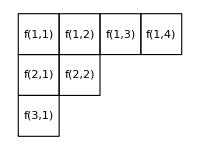

```mathematica
YDGraphDisplayXp[YDConvertCtXp[{4,2,1},f],50]
```

```mathematica
YDGraphDisplayCt[{4,2,1},20]
```

-Graphics-

```mathematica
TableForm[{{YDConvertWfxWvr[{2,1,1,0,0}],YDConvertWfxCt[{2,1,1,0,0}],YDConvertWfxXp[{2,1,1,0,0},f]},{YDConvertWvrWfx[{2,1,1},5],YDConvertWvrCt[{2,1,1}],YDConvertWvrXp[{2,1,1},f]},{YDConvertCtWfx[{4,2,1},5],YDConvertCtWvr[{4,2,1}],YDConvertCtXp[{4,2,1},f]},{YDConvertXpWfx[{{1,2,3,4},{5,6},{7}},5],YDConvertXpWvr[{{1,2,3,4},{5,6},{7}}],YDConvertXpCt[{{1,2,3,4},{5,6},{7}}]}},TableDepth->2]
```

{2,1,1} | {4,2,1} | {{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2]},{f[3,1]}}
{2,1,1,0,0} | {4,2,1} | {{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2]},{f[3,1]}}
{2,1,1,0,0} | {2,1,1} | {{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2]},{f[3,1]}}
{2,1,1,0,0} | {2,1,1} | {4,2,1}

```mathematica
YDRelabelXp[{{1,2,3,4},{5,6},{7}},f]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2]},{f[3,1]}}

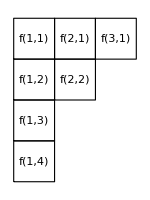

```mathematica
YDGraphDisplayXp[YDTransposeXp[%],50]
```

```mathematica
YDTransposeCt[{4,2,1}]
```

{3,2,1,1}

### Degeneracy (Rep Size)

#### Comparison Tables

```mathematica
(* The table has a value of n for each row and type for each column. Each table entry has a pair of values, one atop the other: the DegenCt value, then the Degen Wfx value (the true value) *)
```

```mathematica
MatAlgList = {"SU(n)","SO(2n)","SO(2n+1)","Sp(2n)"};
```

```mathematica
MatAlgTabDisp[yrls_,nmax_] := TableForm[Table[Table[DegenCtTest[type,yrls,n],{type,MatAlgList}],{n,1,nmax}],TableHeadings->{Automatic,MatAlgList}]
```

```mathematica
MatAlgTabDisp[{3},6]
```

| SU(n) | SO(2n) | SO(2n+1) | Sp(2n)
1 | 4
4 | 2
1 | 7
4 | 4
4
2 | 10
10 | 16
4 | 30
30 | 20
20
3 | 20
20 | 50
50 | 77
77 | 56
56
4 | 35
35 | 112
112 | 156
156 | 120
120
5 | 56
56 | 210
210 | 275
275 | 220
220
6 | 84
84 | 352
352 | 442
442 | 364
364

```mathematica
MatAlgTabDisp[{1,1,1},6]
```

| SU(n) | SO(2n) | SO(2n+1) | Sp(2n)
1 | 0
1 | 0
1 | 1
1 | -2
1
2 | 1
1 | 4
1 | 10
1 | 0
1
3 | 4
4 | 20
4 | 35
8 | 14
14
4 | 10
10 | 56
8 | 84
84 | 48
48
5 | 20
20 | 120
120 | 165
165 | 110
110
6 | 35
35 | 220
220 | 286
286 | 208
208

```mathematica
MatAlgTabDisp[{2,1},6]
```

| SU(n) | SO(2n) | SO(2n+1) | Sp(2n)
1 | 2
2 | 0
1 | 5
2 | 0
2
2 | 8
8 | 16
4 | 35
16 | 16
16
3 | 20
20 | 64
20 | 105
105 | 64
64
4 | 40
40 | 160
160 | 231
231 | 160
160
5 | 70
70 | 320
320 | 429
429 | 320
320
6 | 112
112 | 560
560 | 715
715 | 560
560

```mathematica
MatAlgTabDisp[{2,2},6]
```

| SU(n) | SO(2n) | SO(2n+1) | Sp(2n)
1 | 1
1 | -2
1 | 0
1 | 0
1
2 | 6
6 | 10
3 | 35
10 | 14
14
3 | 20
20 | 84
10 | 168
168 | 90
90
4 | 50
50 | 300
300 | 495
495 | 308
308
5 | 105
105 | 770
770 | 1144
1144 | 780
780
6 | 196
196 | 1638
1638 | 2275
2275 | 1650
1650

#### Symmetric and Antisymmetric Reps

```mathematica
(* Young diagrams for symmetric and antisymmetric tensors *)
```

```mathematica
YDSym[m_] := {m}
```

```mathematica
YDAts[m_] := ConstantArray[1,m]
```

```mathematica
(* From permutations of indices *)
```

```mathematica
DegenSym[m_,n_] := Product[(n+k-1)/k,{k,m}]
```

```mathematica
DegenAts[m_,n_] := Product[(n-k+1)/k,{k,m}]
```

```mathematica
(* Tests *)
```

```mathematica
sanmax = 10;
```

```mathematica
Table[DegenCt["SU(n)",YDSym[m],n] - DegenSym[m,n],{m,1,sanmax}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Sum[DegenCt["SO(n)",YDSym[k],n],{k,m,0,-2}] - DegenSym[m,n],{m,1,sanmax}] // Factor
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[DegenCt["SO(n)",YDSym[m],n] - (DegenCt["SU(n)",YDSym[m],n] - If[m>=2,DegenCt["SU(n)",YDSym[m-2],n] ,0]),{m,1,sanmax}] // Factor
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[DegenCt["Sp(n)",YDSym[m],n] - DegenSym[m,n],{m,1,sanmax}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[DegenCt["SU(n)",YDAts[m],n] - DegenAts[m,n],{m,1,sanmax}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[DegenCt["SO(n)",YDAts[m],n] - DegenAts[m,n],{m,1,sanmax}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Sum[DegenCt["Sp(n)",YDAts[k],n],{k,m,0,-2}] - DegenAts[m,n],{m,1,sanmax}] // Factor
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[DegenCt["Sp(n)",YDAts[m],n] - (DegenCt["SU(n)",YDAts[m],n] - If[m>=2,DegenCt["SU(n)",YDAts[m-2],n] ,0]),{m,1,sanmax}] // Factor
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Note: for SO(n) symmetric and Sp(n) antisymmetric, one subtracts traces relative to the algebra metric: a symmetric one, for SO(n), and an antisymmetric one, for Sp(n). *)
```

#### Riemann curvature tensor

```mathematica
(* Riemann curvature tensor - subtract traceless version (Weyl tensor) *)
```

```mathematica
YDRiemCurv= {2,2};YDGraphDisplayCt[YDRiemCurv,16]
```

-Graphics-

```mathematica
DegenCt["SU(n)",YDRiemCurv,n]
```

1/12 (-1+n) n^2 (1+n)

```mathematica
DegenCt["SO(n)",YDRiemCurv,n]
```

1/12 (-3+n) n (1+n) (2+n)

```mathematica
%% - % // Factor
```

1/2 n (1+n)

```mathematica
(* Difference: Ricci tensor - subtract traceless version *)
```

```mathematica
YDRicCurv= {2};YDGraphDisplayCt[YDRicCurv,16]
```

-Graphics-

```mathematica
DegenCt["SU(n)",YDRicCurv,n]
```

1/2 n (1+n)

```mathematica
DegenCt["SO(n)",YDRicCurv,n]
```

1/2 (-1+n) (2+n)

```mathematica
%%-% // Factor
```

1

```mathematica
(* Remaining one: Ricci scalar *)
```

```mathematica
DegenCt["SU(n)",{},n]
```

1

```mathematica
DegenCt["SO(n)",{},n]
```

1

### YD Products

```mathematica
YDTestDispCt /@ {{1},{2},{1,1}}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{1},{1}]
```

{{1,-Graphics-},{1,-Graphics-}}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{2},{1}]
```

{{1,-Graphics-},{1,-Graphics-}}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{1,1},{1}]
```

{{1,-Graphics-},{1,-Graphics-}}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{2},{2}]
```

{{1,-Graphics-},{1,-Graphics-},{1,-Graphics-}}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{2},{1,1}]
```

{{1,-Graphics-},{1,-Graphics-}}

```mathematica
YDTestMultCntdDispCt @ YDProductCt[{1,1},{1,1}]
```

{{1,-Graphics-},{1,-Graphics-},{1,-Graphics-}}

### YD Vector Powers

```mathematica
TableForm[YDTestMultCntdDispCt /@ VPFindMultDgrmListSeq[4],TableDepth->2]
```

{1,-Graphics-} |  |  |  | 
{1,-Graphics-} | {1,-Graphics-} |  |  | 
{1,-Graphics-} | {2,-Graphics-} | {1,-Graphics-} |  | 
{1,-Graphics-} | {3,-Graphics-} | {2,-Graphics-} | {3,-Graphics-} | {1,-Graphics-}

### Branching Rules

```mathematica
(* SU(n) -> SO(n) -- find traceless parts of tensors *)
```

```mathematica
SUSOSpFwdInvBranching[2]
```

{<|{}→{{1,{}}},{1}→{{1,{1}}},{2}→{{1,{2}},{1,{}}},{1,1}→{{1,{1,1}}}|>,<|{}→{{1,{}}},{1}→{{1,{1}}},{2}→{{-1,{}},{1,{2}}},{1,1}→{{1,{1,1}}}|>}

```mathematica
(* SU(n) -> Sp(n) -- like SO(n) but using the trace relative to the Sp(n) discriminant *)
```

```mathematica
SUSOSpFwdInvBranching[2,True]
```

{<|{}→{{1,{}}},{1}→{{1,{1}}},{2}→{{1,{2}}},{1,1}→{{1,{1,1}},{1,{}}}|>,<|{}→{{1,{}}},{1}→{{1,{1}}},{2}→{{1,{2}}},{1,1}→{{-1,{}},{1,{1,1}}}|>}

### Symmetric and Alternating Group Characters

```mathematica
symgrpchars = SymmGroups[6,True];
```

```mathematica
TestCharsAssoc /@ symgrpchars // Flatten // Union
```

{0}

```mathematica
SymmGroupDisp[x_] := Module[{perms,dgns,chars,ccat,clsslbls,irplbls},
perms = x["Perms"];
dgns = x["Degens"];
chars = x["Chars"];
ccat[z_] := StringRiffle[ToString /@ z,""];
irplbls = ccat /@ perms;
clsslbls = StringRiffle[#,":"]& /@ Transpose[{irplbls,ToString /@ dgns}];
TableForm[chars,TableHeadings->{irplbls,clsslbls}]
]
```

```mathematica
altgrpchars = MakeAltGroup /@ symgrpchars;
```

```mathematica
TestCharsAssoc /@ altgrpchars// Flatten // Union
```

{0}

```mathematica
AltGroupDisp[x_] := Module[{classes,irreps,dgns,chars,ccat,sgn,clsslbls,irplbls},
classes = x["Classes"];
irreps = x["Irreps"];
dgns = x["Degens"];
chars = x["Chars"];
ccat[z_] := StringRiffle[ToString /@ z,""];
sgn[z_] := If[z>=0,"+","-"];
irplbls = If[Length[#]>1,If[Length[Last[#]]>0,StringRiffle[ccat /@ #,","],ccat[#[[1]]]<>sgn[#[[2]]]],"1"]& /@ irreps;
clsslbls = If[Length[#[[1]]]>0,ccat[#[[1]]]<>sgn[#[[2]]],ccat[#]]& /@ classes;
clsslbls = StringRiffle[#,":"]& /@ Transpose[{clsslbls,ToString /@ dgns}];
TableForm[chars,TableHeadings->{irplbls,clsslbls}]
]
```

```mathematica
(* Rows: irreps, columns: classes with degeneracies -- class:degen *)
```

```mathematica
TableForm[Flatten[Table[{"---",i,"Symmetric",SymmGroupDisp[symgrpchars[[i]]],"Alternating",AltGroupDisp[altgrpchars[[i]]]},{i,Length[symgrpchars]}]]]
```

---
1
Symmetric
 | 1:1
1 | 1
Alternating
 | 1:1
1 | 1
---
2
Symmetric
 | 11:1 | 2:1
11 | 1 | 1
2 | 1 | -1
Alternating
 | 11:1
11,2 | 1
---
3
Symmetric
 | 111:1 | 21:3 | 3:2
111 | 1 | 1 | 1
21 | 2 | 0 | -1
3 | 1 | -1 | 1
Alternating
 | 111:1 | 3+:1 | 3-:1
111,3 | 1 | 1 | 1
21+ | 1 | 1/2 (-1+ⅈ √3) | 1/2 (-1-ⅈ √3)
21- | 1 | 1/2 (-1-ⅈ √3) | 1/2 (-1+ⅈ √3)
---
4
Symmetric
 | 1111:1 | 211:6 | 22:3 | 31:8 | 4:6
1111 | 1 | 1 | 1 | 1 | 1
211 | 3 | 1 | -1 | 0 | -1
22 | 2 | 0 | 2 | -1 | 0
31 | 3 | -1 | -1 | 0 | 1
4 | 1 | -1 | 1 | 1 | -1
Alternating
 | 1111:1 | 22:3 | 31+:4 | 31-:4
1111,4 | 1 | 1 | 1 | 1
211,31 | 3 | -1 | 0 | 0
22+ | 1 | 1 | 1/2 (-1+ⅈ √3) | 1/2 (-1-ⅈ √3)
22- | 1 | 1 | 1/2 (-1-ⅈ √3) | 1/2 (-1+ⅈ √3)
---
5
Symmetric
 | 11111:1 | 2111:10 | 221:15 | 311:20 | 32:20 | 41:30 | 5:24
11111 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2111 | 4 | 2 | 0 | 1 | -1 | 0 | -1
221 | 5 | 1 | 1 | -1 | 1 | -1 | 0
311 | 6 | 0 | -2 | 0 | 0 | 0 | 1
32 | 5 | -1 | 1 | -1 | -1 | 1 | 0
41 | 4 | -2 | 0 | 1 | 1 | 0 | -1
5 | 1 | -1 | 1 | 1 | -1 | -1 | 1
Alternating
 | 11111:1 | 221:15 | 311:20 | 5+:12 | 5-:12
11111,5 | 1 | 1 | 1 | 1 | 1
2111,41 | 4 | 0 | 1 | -1 | -1
221,32 | 5 | 1 | -1 | 0 | 0
311+ | 3 | -1 | 0 | 1/2 (1+√5) | 1/2 (1-√5)
311- | 3 | -1 | 0 | 1/2 (1-√5) | 1/2 (1+√5)
---
6
Symmetric
 | 111111:1 | 21111:15 | 2211:45 | 222:15 | 3111:40 | 321:120 | 33:40 | 411:90 | 42:90 | 51:144 | 6:120
111111 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
21111 | 5 | 3 | 1 | -1 | 2 | 0 | -1 | 1 | -1 | 0 | -1
2211 | 9 | 3 | 1 | 3 | 0 | 0 | 0 | -1 | 1 | -1 | 0
222 | 10 | 2 | -2 | -2 | 1 | -1 | 1 | 0 | 0 | 0 | 1
3111 | 5 | 1 | 1 | -3 | -1 | 1 | 2 | -1 | -1 | 0 | 0
321 | 16 | 0 | 0 | 0 | -2 | 0 | -2 | 0 | 0 | 1 | 0
33 | 10 | -2 | -2 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | -1
411 | 5 | -1 | 1 | 3 | -1 | -1 | 2 | 1 | -1 | 0 | 0
42 | 9 | -3 | 1 | -3 | 0 | 0 | 0 | 1 | 1 | -1 | 0
51 | 5 | -3 | 1 | 1 | 2 | 0 | -1 | -1 | -1 | 0 | 1
6 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1
Alternating
 | 111111:1 | 2211:45 | 3111:40 | 33:40 | 42:90 | 51+:72 | 51-:72
111111,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1
21111,51 | 5 | 1 | 2 | -1 | -1 | 0 | 0
2211,42 | 9 | 1 | 0 | 0 | 1 | -1 | -1
222,33 | 10 | -2 | 1 | 1 | 0 | 0 | 0
3111,411 | 5 | 1 | -1 | 2 | -1 | 0 | 0
321+ | 8 | 0 | -1 | -1 | 0 | 1/2 (1+√5) | 1/2 (1-√5)
321- | 8 | 0 | -1 | -1 | 0 | 1/2 (1-√5) | 1/2 (1+√5)

### Symmetric, Schur Functions

```mathematica
xlst = {x1,x2,x3,x4};
```

```mathematica
pslx = PwrSumListFromList[6,xlst]; Take[pslx,2]
```

{x1+x2+x3+x4,x1^2+x2^2+x3^2+x4^2}

```mathematica
(* Elementary symmetric polynomials *)
```

```mathematica
PwrSumToElmSym[Take[pslx,2]]
```

{x1+x2+x3+x4,x1 x2+x1 x3+x2 x3+x1 x4+x2 x4+x3 x4}

```mathematica
ElmSymToPwrSum[PwrSumToElmSym[pslx]]-pslx
```

{0,0,0,0,0,0}

```mathematica
(* Homogeneous symmetric polynomials *)
```

```mathematica
PwrSumToHomSym[Take[pslx,2]]
```

{x1+x2+x3+x4,x1^2+x1 x2+x2^2+x1 x3+x2 x3+x3^2+x1 x4+x2 x4+x3 x4+x4^2}

```mathematica
HomSymToPwrSum[PwrSumToHomSym[pslx]]-pslx
```

{0,0,0,0,0,0}

```mathematica
(* Interchange of these two kinds of polynomials *)
```

```mathematica
ElmSymHomSymItchg[PwrSumToElmSym[pslx]]-PwrSumToHomSym[pslx]
```

{0,0,0,0,0,0}

```mathematica
ElmSymHomSymItchg[PwrSumToHomSym[pslx]]-PwrSumToElmSym[pslx]
```

{0,0,0,0,0,0}

```mathematica
VPFindMultDgrmListSeq[2]
```

{{{1,{1}}},{{1,{2}},{1,{1,1}}}}

```mathematica
(* Compare homogeneous and elementary polynomial formulas to the determinant-formula definition *)
```

```mathematica
SchurHomElmSymVerify[#,xlst]& /@ Flatten[VPFindDgrmListSeq[4],1]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(* Monomial Symmetric Polynomials *)
```

```mathematica
KostkaSchur[2,xlst]
```

{{x1+x2+x3+x4},{x1^2+x2^2+x3^2+x4^2,x1 x2+x1 x3+x2 x3+x1 x4+x2 x4+x3 x4}}

```mathematica
(* Multi-Schur Test *)
```

```mathematica
MultiSchurPowerSumVerify[4,xlst]
```

{{0},{0,0},{0,0,0},{0,0,0,0,0}}

```mathematica
(yds|->Table[SchurProductVerify[yd1,yd2,xlst],{yd1,yds},{yd2,yds}]) @ Flatten[VPFindDgrmListSeq[3],1]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

### Plethysms - Symmetrized Powers

```mathematica
(* Rows are plethysmers: {1}, {2}, {1,1}*)
```

```mathematica
(* Columns are plethysmed ones: {1}, {2}, {1,1} *)
```

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"GenAll",2]]
```

({{1,{1}}} | {{1,{2}}} | {{1,{1,1}}}
{{1,{2}}} | {{1,{4}},{1,{2,2}}} | {{1,{3,1}}}
{{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["Gen",2,"GenAll",2]]
```

({{1,{2}}} | {{1,{1,1}}}
{{1,{4}},{1,{2,2}}} | {{1,{3,1}}}
{{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["SymAll",2,"GenAll",2]]
```

({{1,{1}}} | {{1,{2}}}
{{1,{2}}} | {{1,{4}},{1,{2,2}}}
{{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["Sym",2,"GenAll",2]]
```

({{1,{2}}}
{{1,{4}},{1,{2,2}}}
{{1,{2,2}},{1,{1,1,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["AtsAll",2,"GenAll",2]]
```

((1 | {1}) | (1 | {1,1})
(1 | {2}) | (1 | {3,1})
(1 | {1,1}) | (1 | {2,1,1}))

```mathematica
MatrixForm[SelYDPlethysm["Ats",2,"GenAll",2]]
```

((1 | {1,1})
(1 | {3,1})
(1 | {2,1,1}))

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"GenAll",2]]
```

({{1,{1}}} | {{1,{2}}} | {{1,{1,1}}}
{{1,{2}}} | {{1,{4}},{1,{2,2}}} | {{1,{3,1}}}
{{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"Gen",2]]
```

({{1,{2}}} | {{1,{4}},{1,{2,2}}} | {{1,{3,1}}}
{{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"SymAll",2]]
```

({{1,{1}}} | {{1,{2}}} | {{1,{1,1}}}
{{1,{2}}} | {{1,{4}},{1,{2,2}}} | {{1,{3,1}}})

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"Sym",2]]
```

({{1,{2}}} | {{1,{4}},{1,{2,2}}} | {{1,{3,1}}})

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"AtsAll",2]]
```

({{1,{1}}} | {{1,{2}}} | {{1,{1,1}}}
{{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})

```mathematica
MatrixForm[SelYDPlethysm["GenAll",2,"Ats",2]]
```

({{1,{1,1}}} | {{1,{2,2}},{1,{1,1,1,1}}} | {{1,{2,1,1}}})